```mathematica
Quit[]
```

## Load data

```mathematica
(* Load data first *)
Do[
cohomology[NN]=Import[NotebookDirectory[]<>"cohomology_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
MaxLevel[NN_] := Switch[NN,
2,25,
3,19,
4,15];
NumAllStatesUpToLevel[NN_,level_] := Total[#[[9]]&/@Select[cohomology[NN],#[[1]]<=level&]];
NumAllStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,9]];
NumMultiGravitonStates[NN_,charges_,degree_] := Select[cohomology[NN],#[[2;;6]]==charges&&#[[7]]==degree&][[1,10]];
```

```mathematica
(* Usage example *)
NumAllStates[2,{0,0,4,4,4},7]
NumMultiGravitonStates[2,{0,0,4,4,4},7]
```

1

0

## U(1) partition function

```mathematica
level=25;
ZU1sw[x_,a_,b_,u_,v_,w_]:=(a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b)) x
ZU1B[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]+ZU1sw[-x,a,b,-u,-v,-w])
ZU1F[x_,a_,b_,u_,v_,w_]:=1/2(ZU1sw[x,a,b,u,v,w]-ZU1sw[-x,a,b,-u,-v,-w])

ZU1[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(ZU1B[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n ZU1F[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
ZU1reduced[x_]:=ZU1[1,x^3,x^3,x^2,x^2,x^2]
IU1reduced[x_]:=ZU1[-1,x^3,x^3,-x^2,-x^2,-x^2]
```

## Partition function

```mathematica
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
PermutationMultiplicity[charges_] := Length[Permutations[charges[[1;;2]]]]*Length[Permutations[charges[[3;;5]]]];
Index[NN_,charges_] := Sum[(-1)^(degree+Plus@@charges[[3;;5]]) PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
NumAllStates[NN_,charges_] := Sum[ PermutationMultiplicity[charges]NumAllStates[NN,charges,degree],{degree,2,Total[charges]}]/;ListQ[charges];
Index[NN_,level_] := Sum[Index[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
NumAllStates[NN_,level_] := Sum[NumAllStates[NN,charges],{charges,ChargeList[level]}]/;IntegerQ[level];
Index[NN_] := Index[NN] = Series[(1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
NumAllStates[NN_] :=NumAllStates[NN] = Series[(1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UIndex[NN_] := UIndex[NN] = Series[IU1reduced[x] (1+Sum[Index[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
UNumAllStates[NN_] := UNumAllStates[NN] = Series[ZU1reduced[x] (1+ Sum[NumAllStates[NN,level]x^level,{level,4,MaxLevel[NN]}]),{x,0,MaxLevel[NN]}];
```

```mathematica
UIndex[2]
```

1+3 x^2-2 x^3+9 x^4-6 x^5+11 x^6-6 x^7+9 x^8+14 x^9-21 x^10+36 x^11-17 x^12-18 x^13+114 x^14-194 x^15+258 x^16-168 x^17-112 x^18+630 x^19-1089 x^20+1130 x^21-273 x^22-1632 x^23+4104 x^24-5364 x^25+O[x]^26

```mathematica
Index[2]
```

1+6 x^4-6 x^5-7 x^6+18 x^7+6 x^8-36 x^9+6 x^10+84 x^11-80 x^12-132 x^13+309 x^14-18 x^15-567 x^16+516 x^17+613 x^18-1392 x^19-180 x^20+2884 x^21-1926 x^22-4242 x^23+7890 x^24+792 x^25+O[x]^26

## Graviton partition function

```mathematica
level=25;
f[x_,a_,b_,u_,v_,w_]:=(1+ u)(1+ v)(1+  w)/(1-a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- u(1+ v)(1+ w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x u)/(1-x v)/(1-x w)-1)- v(1+  w)/(1- a)/(1- b)((1+x a)(1+x b)/(1-x v)/(1-x w)-1)-w/(1- a)/(1- b)((1+ x a)(1+x b)/(1-x w)-1)-a b x/(1- a)/(1- b)-((a+b-a b+u+v+w+u v+u w+v w+u v w)/((1-a)(1-b))) x

fB[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]+f[-x,a,b,-u,-v,-w])/2
fF[x_,a_,b_,u_,v_,w_]:=(f[x,a,b,u,v,w]-f[-x,a,b,-u,-v,-w])/2
Zgrav[x_,a_,b_,u_,v_,w_]:=((Series[Exp[Sum[1/n(fB[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]-(-1)^n fF[x^n,a^n t^(3n),b^n t^(3n),u^n t^(2n),v^n t^(2n),w^n t^(2n)]),{n,1,level/2}]],{t,0,level}]//Normal)/.{t->1})
Zgravreduced[x_]:=Zgrav[1,x^3,x^3,x^2,x^2,x^2]
Igravreduced[x_]:=Zgrav[-1,x^3,x^3,-x^2,-x^2,-x^2]

ZUgravreduced[x_]:=Series[ZU1reduced[x]Zgravreduced[x],{x,0,level}]
IUgravreduced[x_]:=Series[IU1reduced[x]Igravreduced[x],{x,0,level}]
```

```mathematica
ZUgravreduced[x]
IUgravreduced[x]
```

1+3 x^2+2 x^3+15 x^4+18 x^5+61 x^6+102 x^7+264 x^8+490 x^9+1107 x^10+2160 x^11+4574 x^12+9018 x^13+18375 x^14+36160 x^15+71931 x^16+140406 x^17+274534 x^18+530754 x^19+1023942 x^20+1960192 x^21+3739383 x^22+7091604 x^23+13396454 x^24+25183602 x^25+O[x]^26

1+3 x^2-2 x^3+9 x^4-6 x^5+21 x^6-18 x^7+48 x^8-42 x^9+99 x^10-96 x^11+200 x^12-198 x^13+381 x^14-396 x^15+711 x^16-750 x^17+1278 x^18-1386 x^19+2256 x^20-2472 x^21+3879 x^22-4320 x^23+6564 x^24-7362 x^25+O[x]^26

## Tables

```mathematica
NN = 2;
StringReplace[Join[{{"Level","SU","SU Index","U", "U Index"}},Join[{Range[0,MaxLevel[NN]]},CoefficientList[{NumAllStates[NN],Index[NN],UNumAllStates[NN],UIndex[NN]},x]]//Transpose]//MatrixForm//TeXForm//ToString,{"\\\\"->"\\\\\\hline"}]
```

\left(
\begin{array}{ccccc}
 \text{Level} & \text{SU} & \text{SU Index} & \text{U} & \text{U Index} \\\hline
 0 & 1 & 1 & 1 & 1 \\\hline
 1 & 0 & 0 & 0 & 0 \\\hline
 2 & 0 & 0 & 3 & 3 \\\hline
 3 & 0 & 0 & 2 & -2 \\\hline
 4 & 6 & 6 & 15 & 9 \\\hline
 5 & 6 & -6 & 18 & -6 \\\hline
 6 & 9 & -7 & 51 & 11 \\\hline
 7 & 18 & 18 & 90 & -6 \\\hline
 8 & 30 & 6 & 195 & 9 \\\hline
 9 & 40 & -36 & 362 & 14 \\\hline
 10 & 66 & 6 & 699 & -21 \\\hline
 11 & 120 & 84 & 1308 & 36 \\\hline
 12 & 198 & -80 & 2431 & -17 \\\hline
 13 & 324 & -132 & 4434 & -18 \\\hline
 14 & 537 & 309 & 8046 & 114 \\\hline
 15 & 822 & -18 & 14346 & -194 \\\hline
 16 & 1257 & -567 & 25434 & 258 \\\hline
 17 & 1944 & 516 & 44544 & -168 \\\hline
 18 & 2959 & 613 & 77442 & -112 \\\hline
 19 & 4476 & -1392 & 133386 & 630 \\\hline
 20 & 6834 & -180 & 228021 & -1089 \\\hline
 21 & 10352 & 2884 & 386898 & 1130 \\\hline
 22 & 15540 & -1926 & 651843 & -273 \\\hline
 23 & 23406 & -4242 & 1091004 & -1632 \\\hline
 24 & 35076 & 7890 & 1814578 & 4104 \\\hline
 25 & 52020 & 792 & 2999724 & -5364 \\\hline
\end{array}
\right)

## Plots

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->24};
SetOptions[ListPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
SetOptions[ListLogLogPlot,{BaseStyle->texStyle, PlotMarkers->{None,Tiny}}];
size = 12;
mag = 1.5;
```

```mathematica
Do[
Export["/Users/yinhslin/git/bh/SU"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[NumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[Index[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["SU("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}},TicksStyle->Directive[Black,size]]];
Export["/Users/yinhslin/git/bh/U"<>ToString[NN]<>".pdf",ListLogPlot[{{Range[0,MaxLevel[NN]],CoefficientList[UNumAllStates[NN],x]}//Transpose,{Range[0,MaxLevel[NN]],Abs[CoefficientList[UIndex[NN],x]]}//Transpose},AxesLabel->{MaTeX["n",Magnification->mag]},PlotLabel->MaTeX["U("<>ToString[NN]<>")",Magnification->mag],PlotStyle->Black,PlotMarkers->{{"●",size},{"○",size}}]];
,{NN,2,4}
]
```

## Load anomalous dimensions

```mathematica
(* Load data first *)
Do[
ad[NN]=Import[NotebookDirectory[]<>"ad_"<>ToString[NN]<>".csv"];
,
{NN,2,4}
];
```

```mathematica
MaxLevel[NN_] := Switch[NN,
2,24,
3,17,
4,15];
OrganizeData[data_]:=Tally[Sort[Flatten[#[[9;;]]&/@data]]];
AD[NN_]:=ad[NN]//OrganizeData;
AD[NN_,charges_]:=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]//OrganizeData];
AD[NN_,charges_,degree_]:=AD[NN,charges,degree]=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&&#[[7]]==degree&]//OrganizeData];
ADUpToLevel[NN_,level_]:=Select[ad[NN],#[[1]]<=level&]//OrganizeData;
charges[level_]:=charges[level]=Flatten[#]&/@DeleteDuplicates[{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers]]
```

```mathematica
ad[NN_,charges_]:=ad[NN,charges]=Module[{c},c=Join[Sort[charges[[1;;2]]],Sort[charges[[3;;5]]]];Select[ad[NN],#[[2;;6]]==c&]];
adAll[NN_]:=adAll[NN]=Flatten[Table[ad[2,c],{l,4,MaxLevel[NN] },{c,charges[l]}],2];
adAll[2];
```

## Characters

```mathematica
χsu2[m_][t_]:=(t^(1/2(2m+1))-t^(-1/2(2m+1)))/(t^(1/2)-t^(-1/2));
χsu3[m1_,m2_][t1_,t2_]:=t1^(m1+2m2)Sum[t1^(-3/2(k+l))(t1^((k-l+1)/2)t2^(-(k-l+1))-t1^(-(k-l+1)/2)t2^((k-l+1)))/(t1^(1/2)t2^-1-t1^(-1/2)t2),{k,m2,m1+m2},{l,0,m2}];
χ[EE_,JL_,JR_,q1_,q2_,q3_]:=Module[{s3,t2},Exp[-β EE-JL(ω1+ω2)-1/3(Δ1+Δ2+Δ3)(q1+q2+q3)]χsu2[JR][Exp[-(ω1-ω2)]]/(1-Exp[-β-ω1])/(1-Exp[-β-ω2])χsu3[q1-q2,q2-q3][Exp[-1/3(2Δ1-Δ2-Δ3)],Exp[-1/3(Δ1+Δ2-2Δ3)]](1+Exp[-1/2(β-ω1-ω2+ Δ1+ Δ2+ Δ3)])(1+Exp[-1/2(β+ω1+ω2- Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1+ω2- Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β+ω1+ω2+ Δ1- Δ2- Δ3)])
(1+Exp[-1/2(β+ω1-ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β+ω1-ω2+ Δ1+ Δ2- Δ3)])
(1+Exp[-1/2(β-ω1+ω2- Δ1+ Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1- Δ2+ Δ3)])
(1+Exp[-1/2(β-ω1+ω2+ Δ1+ Δ2- Δ3)])
];
fugacity={β->-2Log[t0],ω1->-2Log[a]-Log[t0],ω2->-2Log[b]-Log[t0],Δ1->-2Log[u],Δ2->-2Log[v],Δ3->-2Log[w]};
```

## Partition function

```mathematica
ZAtLevel[l_,Δ_]:=ZAtLevel[l,Δ]=Sum[(a b)^(Total[c]-d)(a/ b)^(c[[1]]-c[[2]])u^(c[[3]]-c[[4]]-c[[5]]+d)v^(-c[[3]]+c[[4]]-c[[5]]+d)w^(-c[[3]]-c[[4]]+c[[5]]+d)t0^l ed[[2]],{c,charges[l]},{d,2,Total[c]},{ed,Select[AD[2,c,d],#[[1]]==Δ&]}];
Z[L_,Δ_]:=Sum[ZAtLevel[l,Δ],{l,4,L}];
```

```mathematica
(* TODO: Too Slow *)
```

```mathematica
L=24;
Δ=1.5;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[5/2,1/2,0,1/2,1/2,1/2]+χ[11/2,2/2,1/2,5/2,1/2,1/2]+χ[15/2,3/2,0,7/2,1/2,1/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
L=24;
Δ=0.47546;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[18/2,5/2,1/2,4/2,2/2,2/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
L=24;
Δ=0.75;
Assuming[a>0&&b>0,Z[L,Δ]-Series[χ[13/2,3/2,0/2,3/2,3/2,1/2]+χ[17/2,5/2,0/2,5/2,1/2,1/2]/.fugacity//Simplify,{t0,0,L}]//Simplify]
```

O[t0]^25

```mathematica
primaryCharge[expr_,L_]:=Module[{series,leadingLevel, exp},
series=Series[expr,{t0,0,L}];
leadingLevel=Min[Exponent[Normal[series],t0,List]];
exp=Exponent[Coefficient[series,t0^leadingLevel]//Normal//Expand//First,{a,b,u,v,w}];
{1/2(leadingLevel-(exp[[1]]+exp[[2]])/2),(exp[[1]]+exp[[2]])/4,(exp[[1]]-exp[[2]])/4,exp[[3]]/2,exp[[4]]/2,exp[[5]]/2}
];
primaryCharge[expr_]:=primaryCharge[expr,24];
primaries[expr_,L_]:=Module[{p={},exponent,Z},
Z=expr;
While[((Series[Z,{t0,0,L}]//Normal)/.{t0->1,a->1,b->1,u->1,v->1,w->1})!=0,
exponent=primaryCharge[Z];
AppendTo[p,exponent];
Z=Z-Assuming[a>0&&b>0,Series[χ@@exponent/.fugacity//Simplify,{t0,0,L}]];
];
p
];
primaries[expr_]:=primaries[expr,24];
```

```mathematica
L=24;
res={};
cnt=0;
lis=DeleteCases[ADUpToLevel[2,L][[;;,1]],0];
Monitor[
Do[
cnt+=1;
AppendTo[res,{dd,primaries[Z[L,dd],L]}];,
{dd,lis}]
,ToString[cnt]<>"/"<>ToString[Length[lis]]<>": "<>ToString[dd]
]
```

```mathematica
Do[
Print[{d,primaries[Z[24,d]]}];,
{d,DeleteCases[AD[2][[;;,1]],0]}]
```

{0.47546,{{9,5/2,1/2,2,1,1}}}

{0.75,{{13/2,3/2,0,3/2,3/2,1/2},{17/2,5/2,0,5/2,1/2,1/2}}}

{0.7804,{{7,2,1,1,1,1}}}

{0.82568,{{19/2,5/2,0,3/2,3/2,3/2}}}

{0.85411,{{19/2,5/2,1,5/2,3/2,1/2}}}

{0.8698,{{8,2,0,2,1,1}}}

{0.8871,{{19/2,2,1/2,7/2,3/2,1/2}}}

{0.93193,{{8,2,1,2,1,1}}}

{0.9693,{{19/2,5/2,1,7/2,1/2,1/2}}}

{0.97352,{{9,3,2,1,1,1}}}

{0.99563,{{19/2,5/2,0,3/2,3/2,3/2}}}

{1,{{11/2,3/2,0,3/2,1/2,1/2}}}

{1.00204,{{17/2,5/2,1,3/2,3/2,1/2}}}

{1.02761,{{15/2,2,1/2,3/2,3/2,1/2}}}

{1.03129,{{17/2,2,1/2,7/2,1/2,1/2}}}

{1.12361,{{19/2,5/2,0,5/2,3/2,1/2}}}

{1.125,{{6,3/2,1/2,1,1,1},{19/2,5/2,0,5/2,3/2,1/2}}}

{1.13339,{{9,2,1,3,1,1}}}

{1.14222,{{9,3,1,1,1,1}}}

{1.14276,{{9,5/2,3/2,2,1,1}}}

{1.22935,{{19/2,5/2,1,3/2,3/2,3/2}}}

{1.23226,{{17/2,2,3/2,3/2,3/2,3/2}}}

{1.23814,{{15/2,5/2,1,3/2,1/2,1/2}}}

{1.25826,{{9,2,0,2,2,1}}}

{1.2597,{{8,5/2,1/2,1,1,1}}}

{1.26106,{{19/2,2,1/2,9/2,1/2,1/2}}}

{1.29418,{{13/2,3/2,1,5/2,1/2,1/2}}}

{1.30931,{{8,5/2,3/2,1,1,1}}}

{1.31677,{{17/2,5/2,2,3/2,3/2,1/2}}}

{1.33443,{{19/2,2,3/2,9/2,1/2,1/2}}}

{1.34904,{{8,5/2,1/2,1,1,1}}}

{1.35441,{{17/2,5/2,2,5/2,1/2,1/2}}}

{1.35648,{{19/2,5/2,1,5/2,3/2,1/2}}}

{1.36018,{{19/2,5/2,1,7/2,1/2,1/2}}}

{1.3699,{{19/2,2,1/2,5/2,3/2,3/2}}}

{1.36991,{{7,3/2,3/2,2,1,1},{7,2,1,2,1,0}}}

{1.38269,{{10,2,1,4,1,1}}}

{1.40253,{{10,2,0,4,1,1}}}

{1.40876,{{10,2,2,4,1,1}}}

{1.41427,{{17/2,2,1/2,5/2,3/2,1/2}}}

{1.41443,{{19/2,5/2,2,3/2,3/2,3/2}}}

{1.42432,{{9,5/2,5/2,2,1,1},{9,3,2,2,1,0}}}

{1.43633,{{9,3,1,1,1,1}}}

{1.43756,{{17/2,5/2,0,5/2,1/2,1/2}}}

{1.44167,{{19/2,2,3/2,7/2,3/2,1/2}}}

{1.44713,{{17/2,3/2,1,9/2,1/2,1/2}}}

{1.46949,{{17/2,2,3/2,7/2,1/2,1/2}}}

{1.49385,{{17/2,3,3/2,3/2,1/2,1/2}}}

{1.5,{{5/2,1/2,0,1/2,1/2,1/2},{11/2,1,1/2,5/2,1/2,1/2},{15/2,3/2,0,7/2,1/2,1/2}}}

{1.5004,{{17/2,5/2,1,3/2,3/2,1/2}}}

{1.5119,{{9,5/2,1/2,2,1,1}}}

{1.5197,{{9,5/2,1/2,3,1,0}}}

{1.54223,{{8,2,2,2,1,1},{8,5/2,3/2,2,1,0}}}

{1.57578,{{9,5/2,3/2,2,1,1}}}

{1.58786,{{19/2,5/2,1,5/2,3/2,1/2}}}

{1.58911,{{15/2,2,3/2,5/2,1/2,1/2}}}

{1.59235,{{19/2,2,1/2,5/2,5/2,1/2}}}

{1.5954,{{10,2,1,3,2,1}}}

{1.6107,{{9,5/2,1/2,2,2,0}}}

{1.6198,{{17/2,3/2,0,7/2,3/2,1/2}}}

{1.63779,{{9,2,0,3,1,1}}}

{1.63811,{{13/2,2,1/2,3/2,1/2,1/2}}}

{1.64296,{{9,2,1,3,1,1}}}

{1.64409,{{19/2,5/2,0,3/2,3/2,3/2}}}

{1.64784,{{17/2,5/2,1,5/2,1/2,1/2}}}

{1.65368,{{19/2,5/2,1,7/2,1/2,1/2}}}

{1.67778,{{19/2,2,1/2,7/2,3/2,1/2}}}

{1.68837,{{19/2,5/2,2,5/2,3/2,1/2}}}

{1.73743,{{9,5/2,1/2,2,1,1}}}

{1.74754,{{15/2,2,1/2,5/2,1/2,1/2}}}

{1.74977,{{17/2,2,1/2,5/2,3/2,1/2}}}

{1.77748,{{8,2,1,2,1,1}}}

{1.79696,{{9,3,1,2,1,0}}}

{1.80582,{{9,2,1,3,1,1}}}

{1.8097,{{8,3/2,1/2,3,1,1}}}

{1.82585,{{9,2,1,2,2,1}}}

{1.84172,{{17/2,3,3/2,3/2,1/2,1/2}}}

{1.8553,{{19/2,2,3/2,5/2,3/2,3/2}}}

{1.87442,{{9,2,1,2,2,1}}}

{1.875,{{9/2,1,1/2,3/2,1/2,1/2},{9,2,0,4,1,0}}}

{1.87568,{{7,3/2,1/2,2,1,1}}}

{1.88392,{{19/2,5/2,0,5/2,3/2,1/2}}}

{1.89869,{{15/2,2,3/2,3/2,3/2,1/2}}}

{1.90035,{{10,2,1,4,1,1}}}

{1.90812,{{15/2,3/2,1,3/2,3/2,3/2}}}

{1.90977,{{17/2,5/2,0,3/2,3/2,1/2}}}

{1.9108,{{9,5/2,1/2,2,1,1}}}

{1.91527,{{9,3,2,1,1,1}}}

{1.92834,{{19/2,2,1/2,5/2,3/2,3/2}}}

{1.93237,{{19/2,5/2,2,3/2,3/2,3/2}}}

{1.93294,{{17/2,5/2,2,5/2,1/2,1/2}}}

{1.95366,{{9,5/2,3/2,2,1,1}}}

$Aborted

## Statistics

```mathematica
Gap[tmp_]:=If[Length[tmp]==0,0,If[tmp[[1,1]]==0,If[Length[tmp]==1,0,tmp[[2,1]]],tmp[[1,1]]]];
Gap[NN_,charges_]:=Module[{tmp=AD[NN,charges]},Gap[tmp]];
GapUpToLevel[NN_,level_]:=Module[{tmp=ADUpToLevel[NN,level]},Gap[tmp]];
ChargeList[level_] := Flatten[#]&/@DeleteDuplicates[Map[Sort,{{nzn,nzp},{nθ1,nθ2,nθ3}}/.Solve[3 nzn+3 nzp+2 nθ1+2 nθ2+2 nθ3==level,{nzn,nzp,nθ1,nθ2,nθ3},NonNegativeIntegers],{2}]];
Stats[NN_,charges_]:=Module[{ad=AD[NN,charges],sum=0,dim=0,sumNoneBPS=0,dimNoneBPS=0},
Do[sum+=i[[1]]*i[[2]];dim+=i[[2]];
If[i[[1]]>0,sumNoneBPS+=i[[1]]*i[[2]];dimNoneBPS+=i[[2]]];
,{i,ad}];
{dim,If[dim==0,0,sum/dim],dimNoneBPS,If[dimNoneBPS==0,0,sumNoneBPS/dimNoneBPS],Gap[ad]}
];
```

```mathematica
chargeList=Flatten[Table[ChargeList[l],{l,4,24}],1];
stats=Stats[2,#]&/@ chargeList;
```

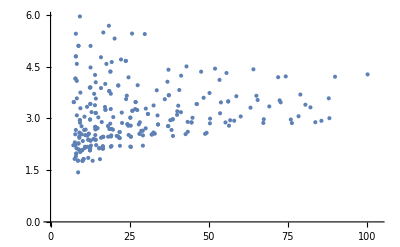

```mathematica
statsX=Select[stats,#[[1]]>=50&];
ListPlot[{Sqrt[#[[1]]],#[[2]]}&/@statsX]
```

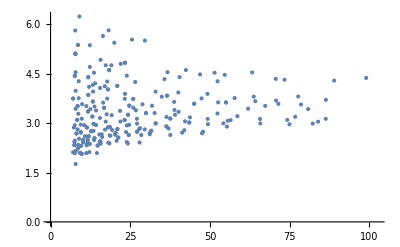

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{Sqrt[#[[3]]],#[[4]]}&/@statsX]
```

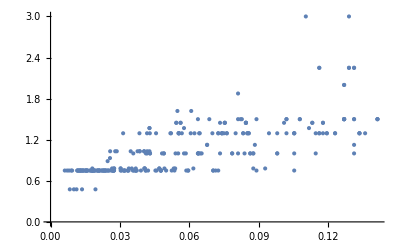

```mathematica
statsX=Select[stats,#[[3]]>=50&];
ListPlot[{1/Sqrt[#[[3]]],#[[5]]}&/@statsX]
```

## Sanity Check

```mathematica
(* Usage example *)
ADUpToLevel[2,24][[1;;5]]
ADUpToLevel[3,16][[1;;5]]
ADUpToLevel[4,15][[1;;5]]
```

{{0,17990},{0.47546,26},{0.75,1302},{0.7804,610},{0.82568,2}}

{{0,2544},{0.83324,8},{0.85942,72},{1.03884,4},{1.1305,4}}

{{0,2051},{0.88412,10},{1.27864,6},{1.29666,16},{1.31934,6}}

```mathematica
(* Sanity check *)
NumAllStatesUpToLevel[2,24]
NumAllStatesUpToLevel[3,16]
NumAllStatesUpToLevel[4,15]
```

17990

2544

2051